## Definitions (Plotting)

```mathematica
(* Graphics *)
R = RegularPolygon[6];
lineThickness=0.03;

δ[1]={0,0};
δ[2]={3/2,-Sqrt[3]/2};
δ[3]={3/2,Sqrt[3]/2};

P[1]={1/2,-(√3)/2};
P[2]=RotationMatrix[2π/3]. (P[1]-{1,0}) + {1,0};
P[3]=RotationMatrix[2 2π/3]. (P[1]-{1,0}) + {1,0};

edgeOrder={
{3,3},
{3,4},
{3,2},
{1,3},
{1,4},
{1,2},
{3,1},
{3,6},
{1,5},
{1,1},
{2,2},
{1,6},
{2,5},
{2,1},
{2,6}};
```

```mathematica
(* i'th edge of a hexagon *)
hexEdge[i_]:=Module[{pts,edge, line},

pts=CirclePoints[6];

edge = {pts[[i]], pts[[Mod[i+1,6,1]]]};

line = {Red,CapForm["Round"],Thickness[lineThickness],Line[edge]};
line
]


(* i'th edge of the h'th hexagon *)
hexEdgeOf[i_, h_]:=Translate[{ hexEdge[i]},δ[h]]
```

```mathematica
(* h'th ancilla - center of hexagon *)
ancilla[h_]:=Module[{point},

point = {Green, Disk[{0,0},0.2]};
point = Translate[{point},δ[h] ];

point

]
```

```mathematica
(* Background *)
bg=Translate[{Blue,Opacity[0.4],RegularPolygon[6]},δ[#]]&/@{1,2,3};
```

```mathematica
spin[σ_,shape_]:=If[σ==0,{},shape]
```

```mathematica
PlotConfiguration[config_,imageSize_:400 ]:=Module[{edges, ancillas},

edges=Table[
With[{σ=config[[s]],hi=edgeOrder[[s]]},
spin[σ,hexEdgeOf[hi[[2]],hi[[1]]]]],
{s,1,15}];

ancillas = Table[
With[{σ=config[[s]]},
spin[σ,ancilla[s-15]]],
{s,16,18}];

Graphics[{bg,edges, ancillas},PlotRange->{{-1.1,2.6},{-1.8,1.8}}, ImageSize->imageSize]

]
```

```mathematica
IndexToConfig[index_Integer,dim_Integer]:=Module[{n},

n=Log[2,dim];

If[!IntegerQ[n],
Message[IndexToConfig::dim,dim];
Return[$Failed];];

IntegerDigits[index-1,2,n]]

IndexToConfig::dim="Dimension `1` is not a power of 2.";


SparseStateToConfigs[psi_SparseArray]:=Module[{dim,rules},
dim=Length[psi];
rules=Most@ArrayRules[psi];

rules/. ({i_}->amp_):>{amp,IndexToConfig[i,dim]}
];
```

```mathematica
StringNetRepresentation[psi_SparseArray]:=Module[{configPairs, stringNetWeights, state},
configPairs = psi // SparseStateToConfigs;

stringNetWeights = {#[[1]],PlotConfiguration[#[[2]],40]}&/@configPairs;

state=Plus@@(#[[1]]Ket[{#[[2]]}]&/@stringNetWeights);

state
]
```

```mathematica
PlotQubitLabels[]:=Module[{edgePositions,centerPositions,txtEdge,txtCenter, figure},
edgePositions={
{"1",{1.5,1.73}},
{"2",{0.75,1.31}},
{"3",{2.24,1.31}},
{"4",{0.,0.87}},
{"5",{-0.77,0.42}},
{"6",{0.75,0.42}},
{"7",{2.23,0.42}},
{"8",{1.5,0}},
{"9",{-0.77,-0.4}},
{"10",{0.75,-0.4}},
{"11",{2.23,-0.4}},
{"12",{0.,-0.87}},
{"13",{0.75,-1.32}},
{"14",{2.23,-1.32}},
{"15",{1.5,-1.73}}
};

centerPositions={
{"16",{0.,0.}},
{"17",{1.5,-0.87}},
{"18",{1.5,0.86}}
};

txtEdge=Graphics[Style[Text[#[[1]],#[[2]]],18, Bold,Yellow]&/@edgePositions];

txtCenter=Graphics[Style[Text[#[[1]],#[[2]]],18, Bold,Blue]&/@centerPositions];

figure = PlotConfiguration[{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}];

Show[{figure,txtEdge,txtCenter},PlotRange->All]
]
```

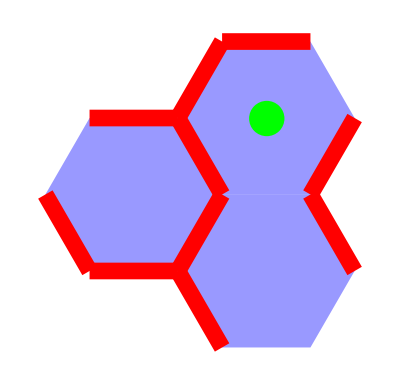

```mathematica
PlotConfiguration[{1,1,0,1,0,1,1,0,1,1,1,1,1,0,0,0,0,1}]
```

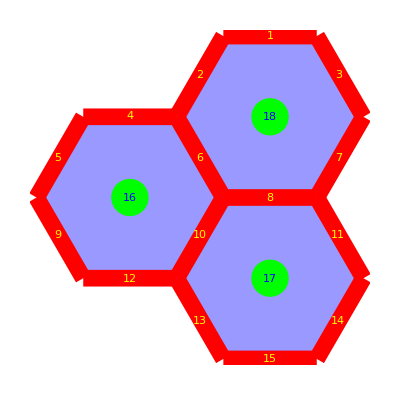

```mathematica
PlotQubitLabels[]
```

```mathematica
SparseArray[{1->a, 2->b,39->c, 2942->d,84448->e, 98282->f},{2^(15+3)}]//StringNetRepresentation
```

a -Graphics-+b -Graphics-+c -Graphics-+d -Graphics-+e -Graphics-+f -Graphics-

## Definitions (calculation)

```mathematica
(* Basis: *)
dim = 2^(15 +3);
```

```mathematica
(* Applies gates {G1,...,Gn} on state psi ---> Gn@...@G1@psi*)
applyGates[gateSequence_][psi_]:=(RightComposition@@gateSequence)[psi]
```

```mathematica
(* Single-qubit gates *)
UsMat:= 1/Sqrt[1+ϕ^2]{{1, ϕ},{ϕ,-1}};
UfMat:= 1/ϕ{{1, Sqrt[ϕ]},{Sqrt[ϕ],-1}};
XMat =PauliMatrix[1];
YMat=PauliMatrix[2];
ZMat=PauliMatrix[3];
```

```mathematica
Clear[OneQGate];

OneQGate[U_,k_Integer?Positive][psi_SparseArray]:=Module[{dim=Length[psi],n,idL,idR,op},
n=Round[Log[2,dim]];
idL=SparseArray[{i_,i_}->1,{2^(k-1),2^(k-1)}];
idR=SparseArray[{i_,i_}->1,{2^(n-k),2^(n-k)}];
op=KroneckerProduct[idL,U,idR];

op.psi];
```

```mathematica
Clear[MultiControlGate];

MultiControlGate[U_?MatrixQ,controls:{__Integer},target_Integer?Positive][psi_SparseArray]:=Module[{dim=Length[psi],n,I2,P1,D,opCond,opTotal,mats},

(*infer number of qubits*)
n=Round[Log[2,dim]];

(*2x2 building blocks*)
I2=SparseArray[{{1,1}->1,{2,2}->1},{2,2}];
(*identity on one qubit*)
P1=SparseArray[{{2,2}->1},{2,2}];
(*projector|1><1|on one qubit*)
D=SparseArray[U-IdentityMatrix[2]];

(*U-I on target qubit*)(*tensor factor for each qubit j=1..n*)mats=Table[
Which[j===target,
D,(*target:U-I*)
MemberQ[controls,j],P1,
(*controls: |1><1|*)
True,
I2 (*others:identity*)
],{j,1,n}];

(*conditional part:only acts when all controls=1*)opCond=KroneckerProduct@@mats;

(*full operator:I+( |1...1>_controls (U-I)_target)*)opTotal=SparseArray[{i_,i_}->1,{dim,dim}]+opCond;

opTotal.psi
];
```

```mathematica
Clear[CX, X, Y, Z, Us, F1]

CX[c_Integer,t_Integer]:=MultiControlGate[XMat,{c},t]
CCX[controls:{__Integer},t_Integer]:=MultiControlGate[XMat,controls,t]

X[q_Integer]:=OneQGate[XMat,q]
Y[q_Integer]:=OneQGate[YMat,q]
Z[q_Integer]:=OneQGate[ZMat,q]
Us[q_Integer]:=OneQGate[UsMat,q]
Uf[q_Integer]:=OneQGate[UfMat,q]

cUf[controls:{__Integer},target_]:=MultiControlGate[UfMat,controls, target]

F1[{a_,b_,c_,d_,e_}]:=Module[{gateSequence},
gateSequence = {cUf[{a,b,c,d},e], CX[d,b], CX[a,c], CCX[{b,c},e],CX[a,c],CX[d,b]};
applyGates[gateSequence]@#&
]

F1[{a_,b_,c_,d_,e_}]:=Module[{gateSequence},
gateSequence = {cUf[{a,b,c,d},e], CX[d,b], CX[a,c], CCX[{b,c},e],CX[a,c],CX[d,b]};
applyGates[gateSequence]@#&
]

Fx[{a_,b_,c_}]:=Module[{gateSequence},
gateSequence = {cUf[{a,c},b], CX[a,c], CX[c,b],CX[a,c]};
applyGates[gateSequence]@#&
]
```

```mathematica
Clear[initializeState];

initializeState[config_]:=Module[{n,dim,ones,psi0},
n=Length[config];
dim=2^n;

(* Positions of 1s in the config list *)ones=Flatten@Position[config,1];

(*|0...0>*)
psi0=SparseArray[{1->1},{dim}];

(*X[i1]@...@X[in]@psi0*)
Fold[X[#2]@#1&,psi0,ones]
]
```

```mathematica
Clear[initializeStateFromOnes];

(* Only give the qubits that should be 1 *)
initializeStateFromOnes[oneQubits_,n_Integer]:=Module[{dim,psi0},
dim=2^n;
psi0=SparseArray[{1->1},{dim}];(* |0...0>*)(*X[i1]@...@X[in]@psi0*)
Fold[X[#2]@#1&,psi0,oneQubits]
];
```

## Tests

```mathematica
psi0=SparseArray[{1->1},{dim}];
```

```mathematica
psi0//ArrayRules
```

{{1}→1,{_}→0}

```mathematica
psi1=Us[1]@psi0;
```

```mathematica
psi2=CX[1,2]@psi1;
```

```mathematica
psi3=CX[1,5]@psi2;
```

```mathematica
psi0//StringNetRepresentation
psi1//StringNetRepresentation
psi2//StringNetRepresentation
psi3//StringNetRepresentation
```

-Graphics-

(-Graphics-)/(√(1+ϕ^2))+(ϕ -Graphics-)/(√(1+ϕ^2))

(-Graphics-)/(√(1+ϕ^2))+(ϕ -Graphics-)/(√(1+ϕ^2))

(-Graphics-)/(√(1+ϕ^2))+(ϕ -Graphics-)/(√(1+ϕ^2))

```mathematica
psi3//StringNetRepresentation
```

(-Graphics-)/(√(1+ϕ^2))+(ϕ -Graphics-)/(√(1+ϕ^2))

```mathematica
singlepsi = ParallelMap[X[#][psi0]&,Range[18]];
```

```mathematica
StringNetRepresentation/@singlepsi
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
gateSequence = {X[1],CX[1,4],Us[5],Us[4],CX[1,4]};
```

```mathematica
applyGates[gateSequence]@psi0//StringNetRepresentation
```

-(-Graphics-)/(1+ϕ^2)-(ϕ -Graphics-)/(1+ϕ^2)+(ϕ -Graphics-)/(1+ϕ^2)+(ϕ^2 -Graphics-)/(1+ϕ^2)

```mathematica
F1[{2,4,6,8,10}]@psi0//StringNetRepresentation
```

-Graphics-

```mathematica
psiA=initializeStateFromOnes[{2,4,6,8,10},18];
psiA//StringNetRepresentation
```

-Graphics-

```mathematica
psiB=initializeStateFromOnes[{2,4,8,10},18];
psiB//StringNetRepresentation
```

-Graphics-

```mathematica
F1[{2,4,8,10,6}]@psiA//StringNetRepresentation
F1[{2,4,8,10,6}]@psiB//StringNetRepresentation
```

(-Graphics-)/(√ϕ)-(-Graphics-)/ϕ

(-Graphics-)/ϕ+(-Graphics-)/(√ϕ)

## Fibonacci Topological order ground-state from Quantum Circuit

```mathematica
plaqA={4,6,10,12,9,5};
plaqB={8,11,14,15,13,10};
plaqC={1,3,7,8,6,2};
ABedge=10;
ACedge=6;
BCedge=8;
cA=16;
cB=17;
cC=18;
```

```mathematica
initializeStateFromOnes[#,18]&/@{Join[plaqA,{cA}],Join[plaqB,{cB}],Join[plaqC,{cC}]}//StringNetRepresentation/@#&
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
initializeStateFromOnes[{13,12,  ACedge,BCedge, ABedge},18]//StringNetRepresentation
```

-Graphics-

```mathematica
gateSequenceA = Join[
{Us[cB]},
 CX[cB,#]&/@plaqB, (* C-NOT fan *)
{CX[BCedge,cB]}
];

gateSequenceB=Join[
{CX[BCedge,cB],Us[cC], CX[cB,BCedge]},
CX[cC,#]&/@Complement[plaqC,{BCedge}], (* C-NOT fan *)
{Fx[{cB,BCedge,cC}],CX[1,cC],CX[15,cB]}
];

gateSequenceC=Join[
{Us[cA],CX[13,ABedge],CX[ACedge,ABedge],CX[2,ACedge],CX[1,cC]},
CX[cA,#]&/@Complement[plaqA,{ABedge,ACedge}], (* C-NOT fan *)
{ Fx[{cA,ACedge,cC}],F1[{12,13,BCedge,ACedge,ABedge}], CX[1,cC],CX[4,cA]}
];
```

```mathematica
(* Initial state *) 
psi0//StringNetRepresentation
```

-Graphics-

```mathematica
(* First plaquette *)
psiA=applyGates[gateSequenceA]@psi0;
psiA//StringNetRepresentation
```

(-Graphics-)/(√(1+ϕ^2))+(ϕ -Graphics-)/(√(1+ϕ^2))

```mathematica
1/Sqrt[ϕ^2+1]/.ϕ->(Sqrt[5]+1)/2//N
ϕ/Sqrt[ϕ^2+1]/.ϕ->(Sqrt[5]+1)/2//N
```

0.525731

0.850651

```mathematica
(* Second plaquette *)
psiB=applyGates[gateSequenceB]@psiA;
psiB//StringNetRepresentation
```

(-Graphics-)/(1+ϕ^2)+(ϕ -Graphics-)/(1+ϕ^2)+(ϕ -Graphics-)/(1+ϕ^2)+(ϕ -Graphics-)/(1+ϕ^2)+(ϕ^(3/2) -Graphics-)/(1+ϕ^2)

```mathematica
1/(ϕ^2+1)/.ϕ->(Sqrt[5]+1)/2//N
ϕ/(ϕ^2+1)/.ϕ->(Sqrt[5]+1)/2//N
ϕ^(3/2)/(ϕ^2+1)/.ϕ->(Sqrt[5]+1)/2//N
```

```mathematica
(* String-net ground-state of doubled Fibonacci model - using a Quantum circuit *)
psiC=applyGates[gateSequenceC]@psiB;
psiC//StringNetRepresentation
```

(-Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(3/2) -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(3/2) -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(3/2) -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(3/2) -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(3/2) -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(3/2) -Graphics-)/((1+ϕ^2)^(3/2))-(ϕ -Graphics-)/((1+ϕ^2)^(3/2))

```mathematica
1/((1+ϕ^2)^(3/2))/.ϕ->(Sqrt[5]+1)/2//N
ϕ/((1+ϕ^2)^(3/2))/.ϕ->(Sqrt[5]+1)/2//N
ϕ^(3/2)/((1+ϕ^2)^(3/2))/.ϕ->(Sqrt[5]+1)/2//N
```

0.145309

0.235114

0.29907

```mathematica
ϕ^2/(1+ϕ^2)/.ϕ->(Sqrt[5]+1)/2//N
```

0.723607

```mathematica
PlotQubitLabels[]
```

-Graphics-

```mathematica
A={a,b,c,d};
```

```mathematica
f[Take[A,#]]&/@Range[Length[A]]
```

{f[{a}],f[{a,b}],f[{a,b,c}],f[{a,b,c,d}]}

```mathematica
PSI =StringNetRepresentation/@ParallelMap[
applyGates[Take[gateSequenceC,#]]@psiB&,Range[0,Length[gateSequenceC]]
];
```

```mathematica
PSI//MatrixForm
```

((-Graphics-)/(1+ϕ^2)+(ϕ -Graphics-)/(1+ϕ^2)+(ϕ -Graphics-)/(1+ϕ^2)+(ϕ -Graphics-)/(1+ϕ^2)+(ϕ^(3/2) -Graphics-)/(1+ϕ^2)
(-Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^2 -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^2 -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^2 -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(3/2) -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(5/2) -Graphics-)/((1+ϕ^2)^(3/2))
(-Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^2 -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^2 -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^2 -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(3/2) -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(5/2) -Graphics-)/((1+ϕ^2)^(3/2))
(-Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^2 -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^2 -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^2 -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(3/2) -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(5/2) -Graphics-)/((1+ϕ^2)^(3/2))
(-Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^2 -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^2 -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^2 -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(3/2) -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(5/2) -Graphics-)/((1+ϕ^2)^(3/2))
(-Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^2 -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^2 -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^2 -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(3/2) -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(5/2) -Graphics-)/((1+ϕ^2)^(3/2))
(-Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^2 -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(3/2) -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^2 -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^2 -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(5/2) -Graphics-)/((1+ϕ^2)^(3/2))
(-Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^2 -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(3/2) -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^2 -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^2 -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(5/2) -Graphics-)/((1+ϕ^2)^(3/2))
(-Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^2 -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(3/2) -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^2 -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^2 -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(5/2) -Graphics-)/((1+ϕ^2)^(3/2))
(-Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^2 -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(3/2) -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^2 -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^2 -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(5/2) -Graphics-)/((1+ϕ^2)^(3/2))
(-Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^2 -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(3/2) -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(3/2) -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(3/2) -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(3/2) -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^2 -Graphics-)/((1+ϕ^2)^(3/2))
(-Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(3/2) -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(3/2) -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(3/2) -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(3/2) -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(3/2) -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(3/2) -Graphics-)/((1+ϕ^2)^(3/2))-(ϕ -Graphics-)/((1+ϕ^2)^(3/2))
(-Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(3/2) -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(3/2) -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(3/2) -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(3/2) -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(3/2) -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(3/2) -Graphics-)/((1+ϕ^2)^(3/2))-(ϕ -Graphics-)/((1+ϕ^2)^(3/2))
(-Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(3/2) -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(3/2) -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(3/2) -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(3/2) -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(3/2) -Graphics-)/((1+ϕ^2)^(3/2))+(ϕ^(3/2) -Graphics-)/((1+ϕ^2)^(3/2))-(ϕ -Graphics-)/((1+ϕ^2)^(3/2)))

```mathematica
Coefficient[#,ϕ]&@PSI[[-1]]
```

(-Graphics-)/((1+ϕ^2)^(3/2))+(-Graphics-)/((1+ϕ^2)^(3/2))+(-Graphics-)/((1+ϕ^2)^(3/2))+(-Graphics-)/((1+ϕ^2)^(3/2))+(-Graphics-)/((1+ϕ^2)^(3/2))+(-Graphics-)/((1+ϕ^2)^(3/2))+(-Graphics-)/((1+ϕ^2)^(3/2))-(-Graphics-)/((1+ϕ^2)^(3/2))

```mathematica
Coefficient[#,ϕ^(3/2)]&@PSI[[-1]]
```

(-Graphics-)/((1+ϕ^2)^(3/2))+(-Graphics-)/((1+ϕ^2)^(3/2))+(-Graphics-)/((1+ϕ^2)^(3/2))+(-Graphics-)/((1+ϕ^2)^(3/2))+(-Graphics-)/((1+ϕ^2)^(3/2))+(-Graphics-)/((1+ϕ^2)^(3/2))

```mathematica
Coefficient[#,ϕ^2]&@PSI[[-1]]
```

0

```mathematica
ϕ^2/(1+ϕ^2)/.ϕ->(Sqrt[5]+1)/2//N
```

0.723607

```mathematica
1/(1+ϕ^2)/.ϕ->(Sqrt[5]+1)/2//N
```

0.276393

```mathematica
ψ1=Normalize@{1,ϕ}/.ϕ->(Sqrt[5]+1)/2//N
#^2&/@ψ1
```

{0.525731,0.850651}

{0.276393,0.723607}

```mathematica
ψ2=Normalize@{1/ϕ,1/Sqrt[ϕ]}/.ϕ->(Sqrt[5]+1)/2//N
#^2&/@ψ2
```

{0.618034,0.786151}

{0.381966,0.618034}

```mathematica
1/Sqrt[1+ϕ^2]{1, 1/ϕ,1/Sqrt[ϕ],1/Sqrt[ϕ],1}/.ϕ->(Sqrt[5]+1)/2//Norm//FullSimplify
```

1

```mathematica
#^2&/@(1/Sqrt[1+ϕ^2]{1, 1/ϕ,1/Sqrt[ϕ],1/Sqrt[ϕ],1})/.ϕ->(Sqrt[5]+1)/2//N
```

{0.276393,0.105573,0.17082,0.17082,0.276393}

```mathematica
#^2&/@(1/Sqrt[1+ϕ^2]{1,1,Sqrt[ϕ]})/.ϕ->(Sqrt[5]+1)/2//N
```

{0.276393,0.276393,0.447214}

```mathematica
(1+ϕ)/(Sqrt[ϕ]ϕ)==Sqrt[ϕ]/.ϕ->(Sqrt[5]+1)/2//FullSimplify
```

True

```mathematica
#^2&/@(1/Sqrt[1+ϕ^2]{1, 1/ϕ+1/Sqrt[ϕ],1/ϕ+1/Sqrt[ϕ]})/.ϕ->(Sqrt[5]+1)/2//N
```

{0.276393,0.544975,0.544975}

```mathematica
(1+1/ϕ+1/Sqrt[ϕ])/Sqrt[1+ϕ^2]/.ϕ->(Sqrt[5]+1)/2//N//#^2&
```

1.59758

```mathematica
1+1/ϕ==ϕ/.ϕ->(Sqrt[5]+1)/2
```

True

```mathematica
1/Sqrt[1+ϕ^2]{1/ϕ,1/Sqrt[ϕ]}/.ϕ->(Sqrt[5]+1)/2//N//Norm
```

0.525731

```mathematica
#^2&/@(1/Sqrt[1+ϕ^2]{1,1/ϕ^2 ,1/(ϕ Sqrt[ϕ]),1/(ϕ Sqrt[ϕ]), 1/(ϕ Sqrt[ϕ]), 1/ϕ,1/ϕ,1/ϕ,1/Sqrt[ϕ]})/.ϕ->(Sqrt[5]+1)/2//N
```

{0.276393,0.0403252,0.0652476,0.0652476,0.0652476,0.105573,0.105573,0.105573,0.17082}

```mathematica
9,
```

```mathematica
1/Sqrt[1+ϕ^2] 1/ϕ^2/.ϕ->(Sqrt[5]+1)/2//N//#^2&
```

0.0403252

```mathematica
1/Sqrt[1+ϕ^2] 1/(ϕ Sqrt@ϕ)/.ϕ->(Sqrt[5]+1)/2//N//#^2&
```

0.0652476

```mathematica
{#,Fibonacci[2 #-1]}&/@Range[10]//MatrixForm
```

(1 | 1
2 | 2
3 | 5
4 | 13
5 | 34
6 | 89
7 | 233
8 | 610
9 | 1597
10 | 4181)

```mathematica
{#,Fibonacci@#}&/@Range[10]
```

{{1,1},{2,1},{3,2},{4,3},{5,5},{6,8},{7,13},{8,21},{9,34},{10,55}}